### M_N samples for N = 64, k = 4, y_0 = 1; data

```mathematica
M4={-0.0425979+I*(0.0908732),0.00101752+I*(0.0247987),-0.099091+I*(0.0518934),-0.0636695+I*(0.0645375),-0.0323864+I*(-0.0569776),0.219111+I*(0.0511027),-0.0817704+I*(0.0343004),-0.158073+I*(0.0626494),0.0210702+I*(0.0500736),-0.123047+I*(0.0540529),-0.187879+I*(0.0398021),-0.0653339+I*(-0.0869128),-0.0778593+I*(-0.108411),0.0208963+I*(0.101076),-0.0110824+I*(-0.21955),-0.076989+I*(0.0746633),0.074377+I*(-0.0440956),0.0955337+I*(0.0209196),-0.131782+I*(-0.0390558),0.0837996+I*(0.0950479),0.0309476+I*(0.0736679),-0.0701345+I*(-0.0282209),-0.224395+I*(0.12388),-0.0437693+I*(-0.18134),0.0286073+I*(0.0526782),0.274771+I*(-0.0984751),0.112328+I*(0.0186044),0.117267+I*(-0.000362829),0.0499464+I*(0.0844294),-0.0809336+I*(0.168186),0.035577+I*(-0.0242281),-0.0730299+I*(-0.051823),-0.00662497+I*(0.00206),0.0150373+I*(0.0635187),0.138182+I*(0.0717641),0.0664245+I*(-0.0672163),0.00584918+I*(-0.00642685),-0.0939925+I*(0.0620017),-0.0510458+I*(0.0327424),-0.0177618+I*(-0.125074),-0.0895947+I*(-0.128509),0.0163411+I*(0.0374791),0.186085+I*(0.0196934),0.0288958+I*(0.0399031),-0.0168963+I*(0.126339),0.0293005+I*(-0.110311),0.0915523+I*(0.0211094),0.0527647+I*(-0.0815348),-0.0825602+I*(0.0571513),-0.0359052+I*(-0.0285648)};
```

### Analysis

```mathematica
(* What we expect for variance at y_0 = 1 *)
```

```mathematica
f[k_] = 1/(4 Pi k) (1 - Exp[- 4 Pi k] );
```

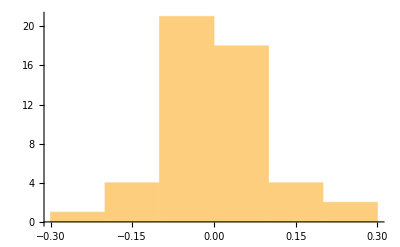

```mathematica
Histogram[Re[M4]]
```

```mathematica
dist = HistogramDistribution[Re[M4]];
```

```mathematica
Moment[dist, 2]
f[4.]/2
```

0.0101333

0.00994718

### M_N samples for N = 256, k = 2, y_0 = 1; data

```mathematica
M2 = {-0.109953+I*(-0.0886159),-0.0855975+I*(-0.149702),-0.105566+I*(0.111289),0.282123+I*(0.161921),0.0714802+I*(-0.0801088),0.170115+I*(-0.191402),-0.0706+I*(-0.257598),-0.0768049+I*(-0.0446059),-0.027664+I*(0.137473),-0.0609348+I*(0.046222),-0.0343407+I*(-0.129554),0.148926+I*(0.153816),-0.247545+I*(-0.172798),-0.0344815+I*(0.00355601),0.26181+I*(0),0.253821+I*(-0.151339),0.110856+I*(0.246048),0.0655049+I*(-0.154651),0.151786+I*(-0.0808494),0.212996+I*(0.0486771),-0.037726+I*(-0.265177),0.129146+I*(-0.0328305),-0.0482397+I*(-0.0228312),0.224035+I*(0.00062429),-0.101552+I*(-0.119019),-0.121531+I*(0.125466),-0.100566+I*(-0.147853),-0.140871+I*(-0.0913633),0.146343+I*(-0.109531),-0.16903+I*(0.101868),0.00991444+I*(0.052859),0.168051+I*(0.0707349),0.246891+I*(0.0259771),0.13773+I*(-0.0648913),-0.115656+I*(-0.0384741),0.0128894+I*(0.0338303),0.010893+I*(0.297572),-0.128014+I*(-0.240706),0.0221862+I*(0.0681682),-0.0776698+I*(-0.060723),0.0448437+I*(-0.0665002),-0.0253205+I*(0.0909648),-0.307613+I*(0.0240617),-0.004208+I*(0.0900566),0.0554057+I*(-0.0502923),0.357087+I*(0.245702),0.0906681+I*(-0.161851),0.105951+I*(0.245738),-0.181646+I*(0.0386116),0.0193109+I*(-0.150508)};
```

### Analysis

```mathematica
(* What we expect for variance at y_0 = 1 *)
```

```mathematica
f[k_] = 1/(4 Pi k) (1 - Exp[- 4 Pi k] );
```

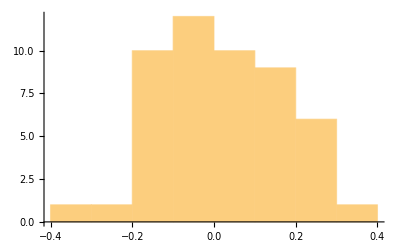

```mathematica
Histogram[Re[M2]]
```

```mathematica
dist2 = HistogramDistribution[Re[M2]];
```

```mathematica
Moment[dist2, 2]
f[2.]/2
```

0.0241333

0.0198943

### M_N samples for N = 256, k = 2, y_0 = 1/2; data

```mathematica
M22={0.16478+I*(-0.149915),-0.278088+I*(0.169923),0.0331309+I*(-0.0753297),0.0730589+I*(0.0571451),0.108551+I*(-0.277514),-0.0971148+I*(0.0159935),0.0136687+I*(-0.00400268),-0.14509+I*(0.0632359),0.347145+I*(-0.0071593),0.199895+I*(-0.340687),-0.133392+I*(-0.0130475),0.0448077+I*(0.285161),0.180244+I*(0.0577717),-0.224394+I*(-0.0803309),0.0331905+I*(-0.0348786),-0.167395+I*(-0.081194),-0.235401+I*(-0.111925),-0.191139+I*(-0.0240292),-0.230247+I*(-0.0525925),-0.162894+I*(0.0195754),-0.0285956+I*(0.0114247),-0.0179274+I*(-0.157825),-0.0702731+I*(-0.173831),0.0495446+I*(-0.204365),-0.153468+I*(-0.197082),0.296696+I*(-0.00262699),0.0107339+I*(-0.0685732),0.0775791+I*(-0.0986314),0.144957+I*(-0.0405338),-0.199677+I*(-0.0724273),0.182586+I*(-0.0446442),0.105931+I*(-0.469263),-0.0688901+I*(-0.0618457),-0.111141+I*(0.152504),-0.0688285+I*(-0.267405),-0.362146+I*(-0.0294481),0.281423+I*(-0.0774024),0.0207807+I*(-0.203811),-0.174091+I*(-0.0693652),-0.0665991+I*(-0.109861),-0.113845+I*(-0.0334093),0.145507+I*(0.0460116),0.307988+I*(0.0484322),-0.0966636+I*(-0.0316106),-0.187723+I*(-0.00274967),0.228835+I*(0.14053),-0.14772+I*(-0.062646),0.0406044+I*(0.257007),0.0141255+I*(0.000674615),0.113287+I*(0.123577)};
```

### Analysis

```mathematica
(* What we expect for variance at y_0 = 1/2 *)
```

```mathematica
f[k_] = 1/(4 Pi k) (1 - Exp[- 2 Pi k] );
```

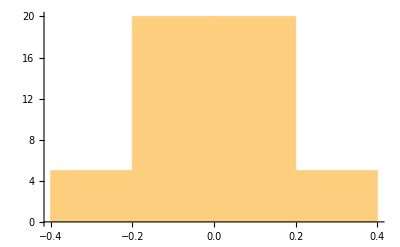

```mathematica
Histogram[Re[M22]]
```

```mathematica
dist22 = HistogramDistribution[Re[M22]];
```

```mathematica
Moment[dist22, 2]
f[2.]/2
```

0.0293333

0.0198943

### M_N samples for N = 256, k = 2, y_0 = 1/4; data

```mathematica
M3={0.16478+I*(-0.149915),-0.278088+I*(0.169923),0.0331309+I*(-0.0753297),0.0730589+I*(0.0571451),0.108551+I*(-0.277514),-0.0971148+I*(0.0159935),0.0136687+I*(-0.00400268),-0.14509+I*(0.0632359),0.347145+I*(-0.0071593),0.199895+I*(-0.340687),-0.133392+I*(-0.0130475),0.0448077+I*(0.285161),0.180244+I*(0.0577717),-0.224394+I*(-0.0803309),0.0331905+I*(-0.0348786),-0.167395+I*(-0.081194),-0.235401+I*(-0.111925),-0.191139+I*(-0.0240292),-0.230247+I*(-0.0525925),-0.162894+I*(0.0195754),-0.0285956+I*(0.0114247),-0.0179274+I*(-0.157825),-0.0702731+I*(-0.173831),0.0495446+I*(-0.204365),-0.153468+I*(-0.197082),0.296696+I*(-0.00262699),0.0107339+I*(-0.0685732),0.0775791+I*(-0.0986314),0.144957+I*(-0.0405338),-0.199677+I*(-0.0724273),0.182586+I*(-0.0446442),0.105931+I*(-0.469263),-0.0688901+I*(-0.0618457),-0.111141+I*(0.152504),-0.0688285+I*(-0.267405),-0.362146+I*(-0.0294481),0.281423+I*(-0.0774024),0.0207807+I*(-0.203811),-0.174091+I*(-0.0693652),-0.0665991+I*(-0.109861),-0.113845+I*(-0.0334093),0.145507+I*(0.0460116),0.307988+I*(0.0484322),-0.0966636+I*(-0.0316106),-0.187723+I*(-0.00274967),0.228835+I*(0.14053),-0.14772+I*(-0.062646),0.0406044+I*(0.257007),0.0141255+I*(0.000674615),0.113287+I*(0.123577)};
```

### Analysis

```mathematica
(* What we expect for variance at y_0 = 1/4 *)
```

```mathematica
f[k_] = 1/(4 Pi k) (1 - Exp[- Pi k] );
```

```mathematica
Histogram[Re[M22]]
```

-Graphics-

```mathematica
dist22 = HistogramDistribution[Re[M22]];
```

```mathematica
Moment[dist22, 2]
f[2.]/2
```

0.0293333

0.0198943

### M_N samples for N = 512, k = 2, y_0 = 1/4; data

```mathematica
M2512={0.0125962+I*(0.142421),-0.0146751+I*(0.172854),-0.00248282+I*(0.186469),0.203383+I*(0.00459569),-0.030221+I*(0.286569),-0.0871208+I*(-0.384672),-0.311316+I*(-0.00303371),-0.0254714+I*(-0.051651),0.115005+I*(0.169232),-0.0930855+I*(-0.0928573),0.0978596+I*(0.163121),0.00932147+I*(0.013135),-0.197252+I*(-0.22179),0.0240718+I*(0.0466852),-0.0805376+I*(0.0989559),-0.171177+I*(-0.027726),-0.103266+I*(0.0409143),0.169458+I*(0.134403),0.169057+I*(-0.115858),-0.0154018+I*(0.195842),0.155926+I*(-0.177784),0.387169+I*(0.118835),-0.0297698+I*(0.0516574),0.0694657+I*(-0.120045),0.0231238+I*(0.0177587),0.232099+I*(-0.0574293),0.0484977+I*(-0.0896962),0.152472+I*(0.15167),-0.173095+I*(0.0591621),0.0681388+I*(0.207552),-0.216219+I*(-0.121586),0.161593+I*(0.174954),0.250309+I*(0.14139),-0.0804477+I*(-0.0733721),-0.0692041+I*(-0.161563),0.105205+I*(0.0919482),0.0266707+I*(-0.122269),0.17517+I*(0.221463),0.0854148+I*(-0.136041),0.0703772+I*(-0.0623949),-0.109547+I*(-0.0338719),0.185509+I*(0.102319),-0.210169+I*(0.0728669),-0.0120841+I*(-0.0775279),0.0925134+I*(-0.0264043),0.0373351+I*(-0.266586),-0.0563144+I*(-0.185809),0.0894269+I*(0.0420452),0.0161485+I*(-0.0796463),-0.0506846+I*(0.10775)};
```

### Analysis

```mathematica
(* What we expect for variance at y_0 = 1/4 *)
```

```mathematica
f[k_] = 1/(4 Pi k) (1 - Exp[- Pi k] );
```

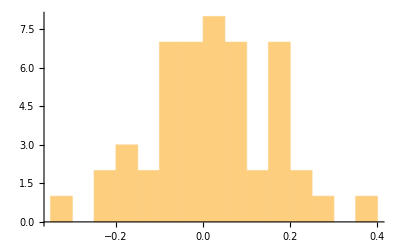

```mathematica
Histogram[Re[M2512], {0.05}]
```

```mathematica
dist222 = HistogramDistribution[Re[M2512]];
```

```mathematica
Moment[dist222, 1]
```

0.018

```mathematica
Moment[dist222, 3]
```

0.00063

```mathematica
Moment[dist222, 2]
f[2.]/2
```

0.0197333

0.0198572

### M_N samples for N = 512, k = 3, y_0 = 1/4; data

```mathematica
M3512={-0.139662+I*(-0.0648115),-0.0563769+I*(0.00526844),0.0545275+I*(0.0418586),-0.0127779+I*(-0.103903),-0.14835+I*(-0.00240133),0.121997+I*(-0.0665263),0.144244+I*(-0.233731),0.132768+I*(0.0573006),0.00506299+I*(-0.0156136),-0.0555491+I*(-0.0422699),0.00908319+I*(-0.159281),0.0407916+I*(-0.220782),-0.0930654+I*(-0.092768),-0.165261+I*(0.00445183),0.157743+I*(0.0425723),0.106363+I*(0.00316235),-0.0615838+I*(-0.18535),-0.031419+I*(-0.0999782),0.075323+I*(-0.101794),0.0587243+I*(-0.0633885),-0.218383+I*(-0.0106235),0.034115+I*(-0.109064),-0.0214755+I*(-0.00738531),-0.0200652+I*(-0.184713),0.123795+I*(0.095689),-0.0252305+I*(0.130168),0.00819025+I*(-0.0141873),-0.0271961+I*(0.0546003),-0.0702734+I*(-0.0524144),0.0309803+I*(-0.126452),0.157024+I*(-0.0306366),-0.134727+I*(-0.19103),0.0459928+I*(-0.142915),-0.176627+I*(-0.201138),0.00202655+I*(-0.158891),-0.272426+I*(0.0827622),-0.000105858+I*(-0.0160208),-0.0332532+I*(0.157028),-0.0643923+I*(0.0718389),-0.0213275+I*(0.213767),0.131755+I*(0.144832),0.0761733+I*(-0.190794),-0.210545+I*(0.0330305),0.106821+I*(0.0768297),0.0720575+I*(0.0352173),-0.112001+I*(0.0657254),0.159499+I*(-0.0958779),0.0148148+I*(0.165071),0.0441951+I*(0.132518),0.0787576+I*(-0.132659)};
```

### Analysis

```mathematica
(* What we expect for variance at y_0 = 1/4 *)
```

```mathematica
f[k_] = 1/(4 Pi k) (1 - Exp[- Pi k] );
```

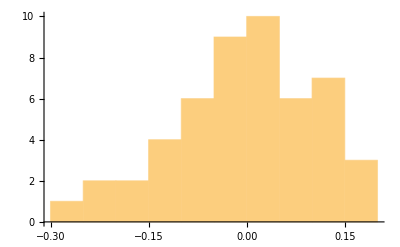

```mathematica
Histogram[Re[M3512], {0.05}]
```

```mathematica
dist3222 = HistogramDistribution[Re[M3512]];
```

```mathematica
Moment[dist3222, 1]
```

-0.002

```mathematica
Moment[dist3222, 3]
```

-0.00067

```mathematica
Moment[dist3222, 2]
f[3.]/2
```

0.0133333

0.0132618

### M_N samples for N = 512, k = 1, y_0 = 1/4; data

```mathematica
M1512={-0.0195789+I*(-0.0988643),0.0129302+I*(-0.290816),0.278851+I*(0.348855),0.0148623+I*(-0.131147),-0.0829098+I*(-0.488595),-0.307184+I*(-0.0543607),0.270717+I*(-0.146233),0.164817+I*(0.285278),-0.0259325+I*(0.118353),-0.160439+I*(-0.360355),0.193045+I*(-0.140764),0.270807+I*(0.0620888),0.101182+I*(-0.011239),-0.0569429+I*(0.413371),0.245429+I*(-0.164344),-0.137216+I*(-0.115902),0.0354865+I*(-0.121008),-0.362796+I*(0.0434127),0.402866+I*(0.486669),0.0765678+I*(0.203611),0.341894+I*(-0.271706),-0.0842152+I*(0.0429833),-0.0196557+I*(-0.13162),0.308402+I*(-0.0281364),0.0898965+I*(0.474213),0.374951+I*(-0.0902157),-0.161555+I*(0.0373142),-0.372204+I*(0.196977),0.044575+I*(-0.0407128),0.350087+I*(0.173418),0.0425848+I*(-0.249813),0.240761+I*(-0.0535549),-0.0724305+I*(0.112551),0.0951187+I*(-0.0549443),-0.0668082+I*(-0.0919619),-0.357482+I*(0.044004),-0.127743+I*(-0.386531),-0.0990809+I*(-0.0212521),0.118152+I*(0.0296985),-0.0460485+I*(0.0504642),0.320387+I*(0.132653),0.285789+I*(0.0625236),0.112347+I*(-0.408639),-0.172425+I*(0.331593),0.0655314+I*(0.327958),-0.153881+I*(0.105341),-0.198795+I*(0.137824),0.321824+I*(0.220667),-0.272819+I*(0.0262275),-0.201992+I*(0.131637)};
```

### Analysis

```mathematica
(* What we expect for variance at y_0 = 1/4 *)
```

```mathematica
f[k_] = 1/(4 Pi k) (1 - Exp[- Pi k] );
```

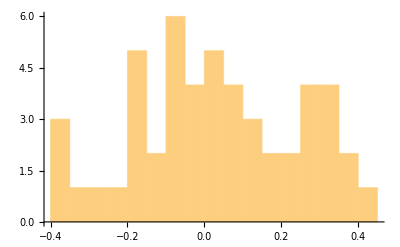

```mathematica
Histogram[Re[M1512], {0.05}]
```

```mathematica
dist1512 = HistogramDistribution[Re[M1512]];
```

```mathematica
Moment[dist1512, 2]
f[1.]/2
```

0.0469333

0.0380693

```mathematica
1/(8 Pi 1.0)
```

0.0397887

### Repeat: M_N samples for N = 512, k = 1, y_0 = 1/4; data

```mathematica
M15122={-0.229618+I*(0.254717),0.0709449+I*(-0.207529),-0.303606+I*(-0.275326),-0.0827454+I*(0.29176),-0.0496959+I*(0.0742357),0.151646+I*(-0.0723658),-0.382795+I*(0.210495),-0.150814+I*(-0.0317607),0.0498115+I*(-0.263651),0.253619+I*(-0.234845),-0.151188+I*(0.0966328),-0.0214161+I*(-0.0686764),-0.0642408+I*(-0.041316),-0.181522+I*(0.435525),-0.099832+I*(0.328728),-0.254477+I*(0.12781),0.0848407+I*(0.246445),-0.267457+I*(0.175),-0.383932+I*(0.339163),0.218804+I*(-0.272358),-0.0513078+I*(-0.238663),0.0945698+I*(-0.216394),-0.183312+I*(0.207751),0.00499326+I*(0.491215),-0.271921+I*(-0.138445),-0.308529+I*(-0.253932),0.147689+I*(-0.162488),0.0878434+I*(0.339388),0.303901+I*(0.390647),0.47392+I*(0.234133),-0.154958+I*(-0.5367),0.233097+I*(0.311642),-0.176396+I*(-0.0270593),0.0835773+I*(0.108931),0.0429111+I*(0.108787),-0.396747+I*(0.065814),0.346698+I*(-0.198046),0.0192379+I*(-0.172543),-0.263581+I*(0.0900027),-0.479724+I*(-0.0370988),0.0146182+I*(-0.0881675),-0.279064+I*(-0.504583),-0.000541868+I*(0.247355),0.433062+I*(-0.0403558),0.1915+I*(0.196327),-0.4465+I*(-0.315038),-0.286309+I*(0.12057),-0.0390015+I*(-0.103296),0.259911+I*(0.31185),-0.173462+I*(-0.243111)};
```

### Analysis

```mathematica
(* What we expect for variance at y_0 = 1/4 *)
```

```mathematica
f[k_] = 1/(4 Pi k) (1 - Exp[- Pi k] );
```

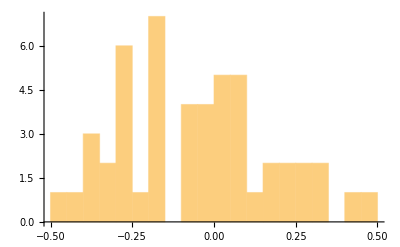

```mathematica
Histogram[Re[M15122], {0.05}]
```

```mathematica
dist11512 = HistogramDistribution[Re[M15122]];
```

```mathematica
Moment[dist11512, 2]
f[1.]/2
```

0.0613333

0.0380693

### M_N samples for N = 512, k = 5, y_0 = 1/4; data

```mathematica
M5512={0.0705574+I*(0.124284),-0.171209+I*(-0.0918727),-0.0505554+I*(-0.0203902),-0.00554627+I*(0.08301),0.0740068+I*(-0.0614291),0.0991651+I*(-0.00771408),-0.104521+I*(-0.0657165),0.115215+I*(-0.0336776),-0.0773077+I*(-0.0963579),-0.13832+I*(0.102627),-0.0707761+I*(0.0683736),0.0652854+I*(-0.108492),0.159668+I*(0.04936),0.0367385+I*(-0.0401758),0.152143+I*(0.089753),0.0398171+I*(0.00807096),0.0480978+I*(-0.0643477),0.0282298+I*(-0.124134),-0.0212823+I*(0.0706201),-0.1325+I*(0.0458967),-0.0743452+I*(-0.0473372),0.0721183+I*(-0.00796763),-0.0412177+I*(-0.0275134),-0.116766+I*(-0.0503457),0.0588056+I*(-0.0408328),-0.0395914+I*(0.0191714),0.151248+I*(-0.00709552),-0.0498803+I*(0.0511183),-0.0521527+I*(0.0633926),0.0818551+I*(0.0592491),-0.015524+I*(0.0963722),-0.0126746+I*(0.00732936),-0.00639673+I*(0.0586955),0.138383+I*(0.014446),-0.0737033+I*(-0.150285),-0.0415648+I*(-0.0154455),-0.0195543+I*(0.0558962),-0.0577564+I*(-0.0362996),0.0486022+I*(0.336048),-0.196908+I*(0.156602),-0.0958044+I*(-0.114467),-0.0238324+I*(-0.100511),0.0196011+I*(0.0409228),-0.00195369+I*(0.0577714),-0.0153826+I*(0.0245253),0.0988353+I*(-0.184629),0.0023813+I*(-0.0165613),0.0371193+I*(0.0847836),0.064603+I*(-0.0031183),-0.172819+I*(0.0707575)};
```

### Analysis

```mathematica
(* What we expect for variance at y_0 = 1/4 *)
```

```mathematica
f[k_] = 1/(4 Pi k) (1 - Exp[- Pi k] );
```

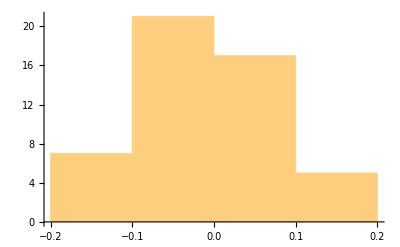

```mathematica
Histogram[Re[M5512]]
```

```mathematica
d1 = HistogramDistribution[Re[M5512]];
```

```mathematica
Moment[d1, 2]
f[5.]/2
```

0.00813333

0.00795775

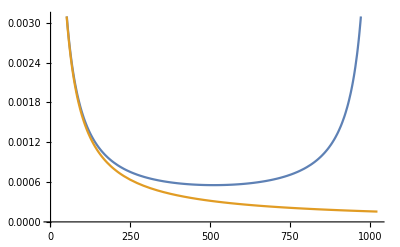

```mathematica
n=2^10;
F[k_]=1/(n ArcCosh[2-Cos[2 Pi k/n]]);
Fc[k_]=1/(2 Pi k);
Plot[{F[k],Fc[k]},{k,1,n}]
```

### M_N samples for N = 512, k = 5, y_ 0 = 1/4, 100 samples; data

```mathematica
M1 ={0.33645+I*(0.0707246),0.165085+I*(0.00137009),-0.195672+I*(0.211347),0.00299318+I*(-0.104152),0.0539437+I*(0.226686),-0.572269+I*(0.434546),-0.0374611+I*(0.142331),0.106589+I*(0.0330549),-0.271722+I*(-0.146245),0.10778+I*(0.243818),-0.310509+I*(0.0684295),0.216232+I*(-0.222854),0.13068+I*(-0.133318),0.0907054+I*(0.0584968),0.0898006+I*(-0.106754),-0.00921577+I*(0.193438),0.159349+I*(0.018925),-0.0812207+I*(-0.316256),0.0978+I*(0.289197),-0.0293309+I*(0.0394823),0.359246+I*(-0.220834),-0.268139+I*(-0.390955),0.0127936+I*(-0.211006),-0.138623+I*(-0.359126),0.23113+I*(0.575149),-0.194772+I*(-0.0395835),-0.0126331+I*(-0.0405639),0.201601+I*(0.0686385),-0.122581+I*(0.186669),0.148173+I*(0.195648),0.000622918+I*(0.0864449),-0.0177808+I*(-0.0271616),0.248162+I*(0.158851),-0.569286+I*(0.101641),-0.304358+I*(-0.120007),-0.056612+I*(0.105499),0.433873+I*(0.0687366),0.0568318+I*(0.0476652),-0.0731088+I*(-0.306355),-0.284885+I*(0.247691),0.0241663+I*(0.179822),0.116168+I*(-0.0806158),0.283814+I*(-0.0701143),-0.290727+I*(0.147578),-0.00733886+I*(-0.142376),-0.339079+I*(0.136034),0.161425+I*(0.0192301),-0.211511+I*(0.235579),-0.403428+I*(0.00326923),-0.337519+I*(0.529706),0.0724219+I*(-0.0311495),-0.263589+I*(0.092538),0.143787+I*(0.183049),-0.345439+I*(-0.0887163),0.117951+I*(-0.0493513),-0.293254+I*(0.00788804),0.298328+I*(0.110242),-0.14253+I*(-0.0150816),-0.0859252+I*(0.247421),-0.0663548+I*(0.0729513),-0.0729124+I*(-0.127918),0.101245+I*(0.50034),-0.0159791+I*(-0.0907974),-0.164407+I*(0.225498),0.145486+I*(-0.123243),0.0866402+I*(0.00666133),0.32574+I*(0.0213748),-0.261232+I*(-0.0550828),-0.0707432+I*(0.0533277),0.212884+I*(-0.100042),0.45677+I*(-0.119034),0.0913917+I*(-0.195194),0.240761+I*(0.37091),-0.160704+I*(0.0280305),0.0180132+I*(-0.119315),0.177387+I*(-0.0145936),0.131147+I*(0.0123792),-0.381438+I*(0.0524592),-0.164884+I*(-0.056983),-0.0824953+I*(0.20779),-0.196627+I*(-0.0314923),0.249144+I*(-0.416191),-0.188268+I*(-0.285143),-0.100416+I*(-0.182488),0.0525182+I*(0.403802),0.267674+I*(-0.0632565),0.171828+I*(-0.14073),0.0277893+I*(-0.387736),-0.045529+I*(-0.100088),0.0273959+I*(0.197945),-0.32629+I*(-0.070945),0.0257077+I*(-0.131715),0.0997875+I*(0.0581026),0.214692+I*(0.159167),-0.0404741+I*(-0.144735),0.0856926+I*(0.262135),-0.400982+I*(0.0967362),-0.290329+I*(-0.180142),-0.181901+I*(-0.0561702),-0.274484+I*(0.382992)};
```

### Analysis

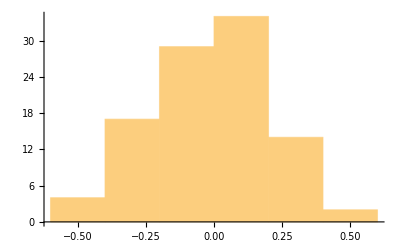

```mathematica
(* What we expect for variance at y_0 = 1/4 *)
f[k_] = 1/(4 Pi k) (1 - Exp[- Pi k] );
Histogram[Re[M1]]
d11 = HistogramDistribution[Re[M1]];
```

```mathematica
Moment[d11, 2]
f[1.]/2
```

0.0525333

0.0380693

### M_N samples for N = 512, k = 5, y_ 0 = 1/4, 100 samples; data

```mathematica
M7 ={-0.0529563+I*(0.0630645),-0.132712+I*(-0.0270225),0.0263071+I*(-0.0273664),0.0300079+I*(-0.051859),-0.0218686+I*(0.0821448),-0.0227145+I*(0.0823648),0.0304948+I*(-0.00950342),-0.00434616+I*(-0.0641638),0.0781692+I*(0.102789),0.0144893+I*(0.0528312),0.0676508+I*(0.11607),0.107437+I*(-0.124059),0.0727662+I*(0.0460702),0.0551443+I*(-0.0834842),0.0104851+I*(-0.0719232),0.000533663+I*(-0.159333),-0.0210994+I*(0.00119256),0.0796379+I*(-0.0401723),-0.0297971+I*(-0.0343386),-0.0328853+I*(-0.0879359),-0.0755336+I*(-0.111243),-0.102215+I*(0.0856543),-0.047974+I*(-0.0214657),0.119086+I*(0.0710897),0.0769177+I*(0.0521243),0.00869843+I*(0.0130741),0.0390235+I*(0.0581405),0.0226573+I*(-0.0306961),0.0205097+I*(0.0669936),-0.00800494+I*(0.0918386),0.0233415+I*(0.0832157),0.111863+I*(0.0853357),-0.00984706+I*(0.0804511),-0.0338594+I*(0.113967),-0.166295+I*(0.00805686),0.0716758+I*(-0.105583),-0.00622617+I*(-0.03721),0.0108378+I*(-0.106419),0.0312468+I*(-0.0220973),0.0607176+I*(-0.107378),-0.092406+I*(0.0937954),-0.0721205+I*(-0.0339208),0.0434982+I*(-0.15817),0.0371188+I*(-0.0707472),-0.015876+I*(0.0616326),0.0471524+I*(0.044626),0.0535566+I*(0.209317),0.12741+I*(-0.0655399),0.146761+I*(-0.0838583),-0.128033+I*(0.0137033),-0.0849892+I*(-0.0295038),0.0461478+I*(0.0305736),-0.0533698+I*(-0.0141833),-0.0100535+I*(-0.030186),0.171027+I*(-0.0967194),-0.0230453+I*(-0.0611819),-0.00637464+I*(0.0705022),-0.073039+I*(0.0469786),-0.0899895+I*(-0.110309),-0.052755+I*(0.0225806),0.152797+I*(-0.0209253),0.0886608+I*(0.226532),0.0250859+I*(0.0284763),0.032044+I*(-0.0132756),0.100637+I*(0.0130102),0.0261393+I*(0.169262),-0.0468965+I*(-0.041079),0.0188167+I*(0.0660424),0.0349623+I*(0.00560328),0.0140949+I*(-0.0335957),-0.0708268+I*(0.0368074),-0.000366593+I*(0.0165601),0.0969328+I*(0.0492164),0.12721+I*(-0.0850028),-0.00566189+I*(0.158297),0.0886217+I*(0.00151245),0.0617732+I*(-0.109693),0.0612555+I*(-0.0856023),-0.0648665+I*(-0.00153476),-0.0314576+I*(0.0432575),0.0280279+I*(0.052779),0.0183624+I*(0.00937189),0.00303404+I*(0.0555868),0.00327324+I*(0.0224405),0.120561+I*(-0.0369744),-0.0917403+I*(0.0265807),-0.0137031+I*(0.0271989),-0.0165812+I*(-0.0851417),-0.0709168+I*(0.0637841),-0.0129296+I*(0.0666313),0.0804789+I*(-0.0424522),0.0957351+I*(-0.00164149),-0.0641606+I*(0.0208238),-0.149734+I*(-0.0808255),0.0113173+I*(-0.0297302),0.00329418+I*(0.0759899),-0.0408744+I*(-0.0441947),-0.113924+I*(-0.0919402),-0.0424448+I*(0.0710582),0.0559822+I*(-0.0567441)};
```

### Analysis

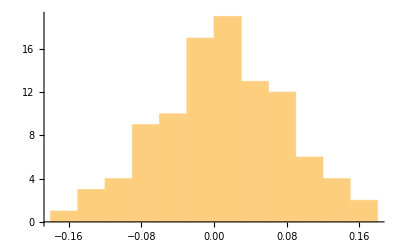

```mathematica
(* What we expect for variance at y_0 = 1/4 *)
f[k_] = 1/(4 Pi k) (1 - Exp[- Pi k] );
Histogram[Re[M7], {0.03}]
d7 = HistogramDistribution[Re[M7]];
```

```mathematica
Moment[d7, 2]
f[7.]/2
```

0.00523333

0.00568411

```mathematica
d7i = HistogramDistribution[Im[M7]];
```

```mathematica
Moment[d7i, 2]
f[7.]/2
```

0.00648333

0.00568411